```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot,ListLogPlot};
SetDirectory["C:\\Users\\akandra\\Projects\\Kinetic Monte Carlo\\kmc\\data\\mmc"]
```

C:\Users\akandra\Projects\Kinetic Monte Carlo\kmc\data\mmc

```mathematica
{TogglerBar[Dynamic[cfiles],FileNames["*.confs"],Appearance->"Vertical"],TogglerBar[Dynamic[efiles],FileNames["*.en"],Appearance->"Vertical"],TogglerBar[Dynamic[hfiles],FileNames["*.hist"],Appearance->"Vertical"]}
```

{






,






,


}

```mathematica
data=Import[#,"Table"]&/@cfiles;
{nlat,nads}=data[[All,1]]ᵀ
occs=Table[Partition[data[[i,2;;]],nlat[[i]]],{i,Length[data]}];
nframes=Length/@occs
```

{{100,100},{2500,2500}}

{11,1001}

```mathematica
energy=Import[#,"Table"]&/@efiles;
```

```mathematica
data=Import["mmc_0100_0250_1000_eq.confs","Table"];
{nlat,nads}=data[[1]]
occs=Partition[data[[2;;]],nlat];
nframes=Length[occs]
```

{100,2500}

11

```mathematica
energy=Import["mmc_0100_0250_1000_eq.en","List"];
```

```mathematica
data=Import["mmc_0100_0250_1000.hist","Table"];
nhsteps=Flatten[data[[;;;;2]]];
hist=data[[2;;;;2]];
```

```mathematica
data=Import["mmc_0100_0250_1000.confs","Table"];
{nlat2,nads2}=data[[1]]
occs2=Partition[data[[2;;]],nlat2];
nframes2=Length[occs2]
```

{100,2500}

1001

```mathematica
energy2=Import["mmc_0100_0250_1000.en","List"];
```

```mathematica
data=Import["mmc_0100_0250_1000.hist","Table"];
nhsteps=Flatten[data[[;;;;2]]];
hist=data[[2;;;;2]];
```

```mathematica
data=Import["mmc_0100_0250_1000_0.confs","Table"];
{nlat3,nads3}=data[[1]]
occs3=Partition[data[[2;;]],nlat2];
nframes3=Length[occs3]
```

{100,2500}

1001

```mathematica
energy3=Import["mmc_0100_0250_1000_0.en","List"];
```

```mathematica
data=Import["mmc_0100_0250_1000_0.hist","Table"];
nhsteps3=Flatten[data[[;;;;2]]];
hist3=data[[2;;;;2]];
```

```mathematica
data=Import["mmc_0100_0250_1000.hist","Table"];
nhsteps=Flatten[data[[;;;;2]]];
hist=data[[2;;;;2]];
```

```mathematica
data=Import["mmc_0100_0250_0400_eq.confs","Table"];
{nlat4,nads4}=data[[1]]
occs4=Partition[data[[2;;]],nlat2];
nframes4=Length[occs4]
```

{100,2500}

11

```mathematica
energy4=Import["mmc_0100_0250_0400_eq.en","List"];
```

```mathematica
data=Import["mmc_0100_0250_0400_2.confs","Table"];
{nlat5,nads5}=data[[1]]
occs5=Partition[data[[2;;]],nlat5];
nframes5=Length[occs5]
```

{100,2500}

1001

```mathematica
energy5=Import["mmc_0100_0250_0400_2.en","List"];
```

```mathematica
data=Import["mmc_0100_0250_0400_2.hist","Table"];
nhsteps5=Flatten[data[[;;;;2]]];
hist5=data[[2;;;;2]];
```

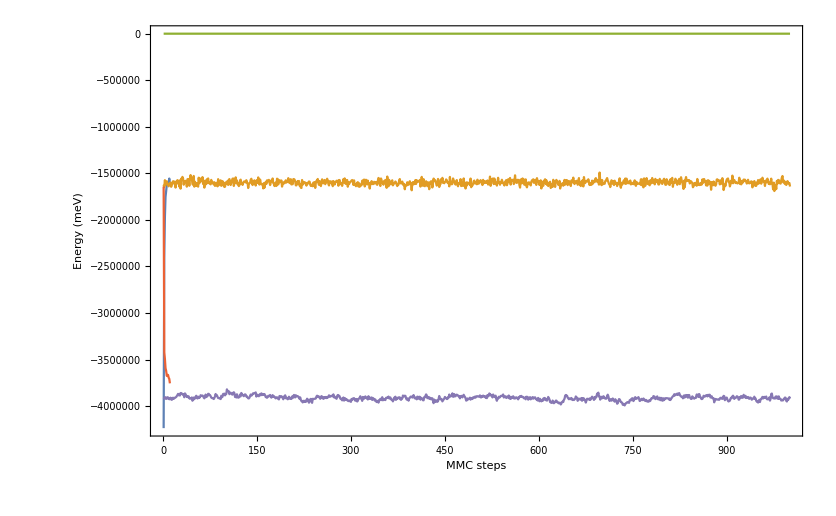

```mathematica
ListLinePlot[{energy,energy2,energy3,energy4,energy5},PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"}]
```

```mathematica
size=Range[1,Length[hist[[-1]]]];
```

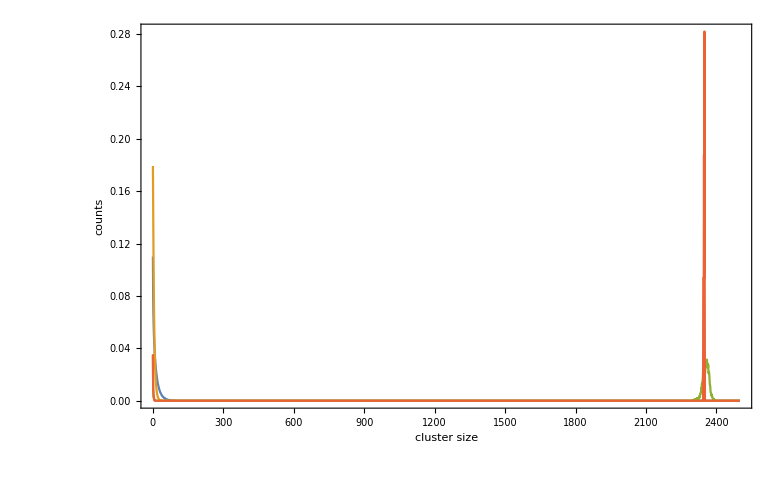

```mathematica
ListLinePlot[{(size hist[[-1]])/(nhsteps[[-1]]nads2),(size hist3[[-1]])/(nhsteps3[[-1]]nads3),(size hist5[[-1]])/(nhsteps5[[-1]]nads5),(size hist5[[1]])/(nhsteps5[[1]]nads5)},FrameLabel->{"cluster size","counts"},PlotRange->{All,All}]
```

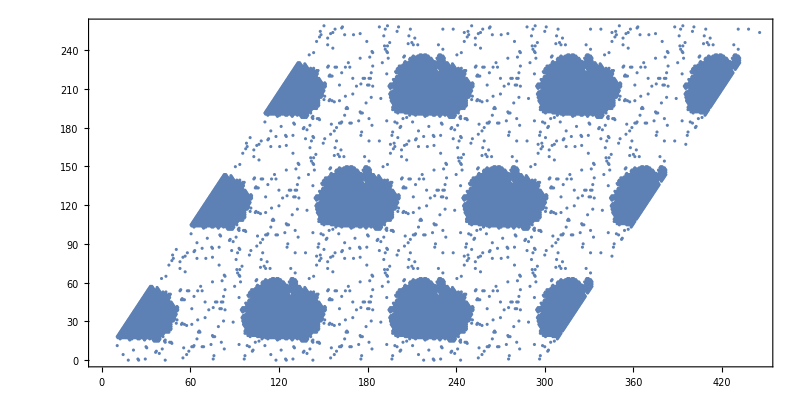

```mathematica
ListPlot[(((#-{1,1})&/@Position[ArrayPad[occs5[[-1]],nlat,"Periodic"],1]).{{1,0},{Cos[π/3],Sin[π/3]}}),AspectRatio->Cos[π/3]]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs5[[i]],nlat,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs3[[i]],0,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```